```mathematica
rollMatrix = RotationMatrix[roll, {1, 0, 0}];
pitchMatrix = RotationMatrix[pitch, {0, 1, 0}];
Rb = rollMatrix . pitchMatrix;
Rb = pitchMatrix.rollMatrix ;
```

```mathematica
sVec = {Sx, Sy, 0};
tVec = {Tx, Ty};
eVec = {Ex, Ey, Ez};
cVec = {Cx, Cy, Cz};
Rbc = {{0,0,1}, {0,-1,0}, {1,0,0}};
```

```mathematica
Rc = Rb . Rbc;
sC = Transpose[Rc].(sVec - cVec);
Target = eVec[[1;;2]] + (sC[[1;;2]] -  eVec[[1;;2]] )*(-eVec[[3]]/(sC[[3]] -eVec[[3] ]));
Ssolution =Solve[Target== tVec, {Sx, Sy}];
```

```mathematica
Simplify[Ssolution, pitch == 0 && roll == 0]
```

{{Sx→(Cx (Ex-Tx)-Ez (Cz+Tx))/(Ex-Tx),Sy→(Cy Ex+Cz Ey-Cy Tx+Ey Tx-Cz Ty-Ex Ty)/(Ex-Tx)}}

```mathematica
Target
```

{Ex-(Ez (-Ex-Cz Cos[pitch] Cos[roll]+(-Cx+Sx) Sin[pitch]-(-Cy+Sy) Cos[pitch] Sin[roll]))/(-Ez+(-Cx+Sx) Cos[pitch]+Cz Cos[roll] Sin[pitch]+(-Cy+Sy) Sin[pitch] Sin[roll]),Ey-(Ez (-Ey-(-Cy+Sy) Cos[roll]+Cz Sin[roll]))/(-Ez+(-Cx+Sx) Cos[pitch]+Cz Cos[roll] Sin[pitch]+(-Cy+Sy) Sin[pitch] Sin[roll])}

```mathematica
Simplify[Target, pitch == 0 && roll ==0]
```

{(Cx Ex-Cz Ez-Ex Sx)/(Cx+Ez-Sx),(Cx Ey+Cy Ez-Ey Sx-Ez Sy)/(Cx+Ez-Sx)}

```mathematica
Simplify[Ey*(Cx+Ez-Sx)-Ez*(-Cy+Ey+Sy)]
```

Cx Ey+Cy Ez-Ey Sx-Ez Sy

```mathematica
{Cx, Cy, Cz} =.;
{Ex, Ey, Ez} =.;
{Tx, Ty} =.;
```

```mathematica
Simplify[Ssolution, roll==0 && pitch == 0 &&Tx == 0.03225 && Ty== 0.06039 
&& Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853]
```

{{Sx→1.65743,Sy→0.521259}}

```mathematica
Target
```

{Ex-(Ez (-Ex-Cz Cos[pitch] Cos[roll]+(-Cx+Sx) Sin[pitch]-(-Cy+Sy) Cos[pitch] Sin[roll]))/(-Ez+(-Cx+Sx) Cos[pitch]+Cz Cos[roll] Sin[pitch]+(-Cy+Sy) Sin[pitch] Sin[roll]),Ey-(Ez (-Ey-(-Cy+Sy) Cos[roll]+Cz Sin[roll]))/(-Ez+(-Cx+Sx) Cos[pitch]+Cz Cos[roll] Sin[pitch]+(-Cy+Sy) Sin[pitch] Sin[roll])}

```mathematica
FullSimplify[Target - tVec =={0,0}]
```

{Ex-Tx-(Ez (Ex+(Cx-Sx) Sin[pitch]+Cos[pitch] (Cz Cos[roll]+(-Cy+Sy) Sin[roll])))/(Ez+(Cx-Sx) Cos[pitch]-Cz Cos[roll] Sin[pitch]+(Cy-Sy) Sin[pitch] Sin[roll]),Ey-Ty+(Ez (-Ey+(Cy-Sy) Cos[roll]+Cz Sin[roll]))/(Ez+(Cx-Sx) Cos[pitch]-Cz Cos[roll] Sin[pitch]+(Cy-Sy) Sin[pitch] Sin[roll])}=={0,0}

```mathematica
StEq = Together[Target - tVec]
```

{(-Ez Tx+Cx Ex Cos[pitch]-Ex Sx Cos[pitch]-Cx Tx Cos[pitch]+Sx Tx Cos[pitch]-Cz Ez Cos[pitch] Cos[roll]-Cx Ez Sin[pitch]+Ez Sx Sin[pitch]-Cz Ex Cos[roll] Sin[pitch]+Cz Tx Cos[roll] Sin[pitch]+Cy Ez Cos[pitch] Sin[roll]-Ez Sy Cos[pitch] Sin[roll]+Cy Ex Sin[pitch] Sin[roll]-Ex Sy Sin[pitch] Sin[roll]-Cy Tx Sin[pitch] Sin[roll]+Sy Tx Sin[pitch] Sin[roll])/(Ez+Cx Cos[pitch]-Sx Cos[pitch]-Cz Cos[roll] Sin[pitch]+Cy Sin[pitch] Sin[roll]-Sy Sin[pitch] Sin[roll]),(-Ez Ty+Cx Ey Cos[pitch]-Ey Sx Cos[pitch]-Cx Ty Cos[pitch]+Sx Ty Cos[pitch]+Cy Ez Cos[roll]-Ez Sy Cos[roll]-Cz Ey Cos[roll] Sin[pitch]+Cz Ty Cos[roll] Sin[pitch]+Cz Ez Sin[roll]+Cy Ey Sin[pitch] Sin[roll]-Ey Sy Sin[pitch] Sin[roll]-Cy Ty Sin[pitch] Sin[roll]+Sy Ty Sin[pitch] Sin[roll])/(Ez+Cx Cos[pitch]-Sx Cos[pitch]-Cz Cos[roll] Sin[pitch]+Cy Sin[pitch] Sin[roll]-Sy Sin[pitch] Sin[roll])}

```mathematica
StEq = Numerator[StEq]
```

{-Ez Tx+Cx Ex Cos[pitch]-Ex Sx Cos[pitch]-Cx Tx Cos[pitch]+Sx Tx Cos[pitch]-Cz Ez Cos[pitch] Cos[roll]-Cx Ez Sin[pitch]+Ez Sx Sin[pitch]-Cz Ex Cos[roll] Sin[pitch]+Cz Tx Cos[roll] Sin[pitch]+Cy Ez Cos[pitch] Sin[roll]-Ez Sy Cos[pitch] Sin[roll]+Cy Ex Sin[pitch] Sin[roll]-Ex Sy Sin[pitch] Sin[roll]-Cy Tx Sin[pitch] Sin[roll]+Sy Tx Sin[pitch] Sin[roll],-Ez Ty+Cx Ey Cos[pitch]-Ey Sx Cos[pitch]-Cx Ty Cos[pitch]+Sx Ty Cos[pitch]+Cy Ez Cos[roll]-Ez Sy Cos[roll]-Cz Ey Cos[roll] Sin[pitch]+Cz Ty Cos[roll] Sin[pitch]+Cz Ez Sin[roll]+Cy Ey Sin[pitch] Sin[roll]-Ey Sy Sin[pitch] Sin[roll]-Cy Ty Sin[pitch] Sin[roll]+Sy Ty Sin[pitch] Sin[roll]}

```mathematica
StEq
```

{-Ez Tx+Cx Ex Cos[pitch]-Ex Sx Cos[pitch]-Cx Tx Cos[pitch]+Sx Tx Cos[pitch]-Cz Ez Cos[pitch] Cos[roll]-Cx Ez Sin[pitch]+Ez Sx Sin[pitch]-Cz Ex Cos[roll] Sin[pitch]+Cz Tx Cos[roll] Sin[pitch]+Cy Ez Cos[pitch] Sin[roll]-Ez Sy Cos[pitch] Sin[roll]+Cy Ex Sin[pitch] Sin[roll]-Ex Sy Sin[pitch] Sin[roll]-Cy Tx Sin[pitch] Sin[roll]+Sy Tx Sin[pitch] Sin[roll],-Ez Ty+Cx Ey Cos[pitch]-Ey Sx Cos[pitch]-Cx Ty Cos[pitch]+Sx Ty Cos[pitch]+Cy Ez Cos[roll]-Ez Sy Cos[roll]-Cz Ey Cos[roll] Sin[pitch]+Cz Ty Cos[roll] Sin[pitch]+Cz Ez Sin[roll]+Cy Ey Sin[pitch] Sin[roll]-Ey Sy Sin[pitch] Sin[roll]-Cy Ty Sin[pitch] Sin[roll]+Sy Ty Sin[pitch] Sin[roll]}

```mathematica
ScoeffX = Coefficient[StEq[[1]],{Sx, Sy}]
```

{-Ex Cos[pitch]+Tx Cos[pitch]+Ez Sin[pitch],-Ez Cos[pitch] Sin[roll]-Ex Sin[pitch] Sin[roll]+Tx Sin[pitch] Sin[roll]}

```mathematica
ScoeffY = Coefficient[StEq[[2]], {Sx, Sy}]
```

{-Ey Cos[pitch]+Ty Cos[pitch],-Ez Cos[roll]-Ey Sin[pitch] Sin[roll]+Ty Sin[pitch] Sin[roll]}

```mathematica
biasX = StEq[[1]] - Dot[ScoeffX , {Sx, Sy}]
biasY = StEq[[2]] - Dot[ScoeffY, {Sx, Sy}]
```

-Ez Tx+Cx Ex Cos[pitch]-Ex Sx Cos[pitch]-Cx Tx Cos[pitch]+Sx Tx Cos[pitch]-Cz Ez Cos[pitch] Cos[roll]-Cx Ez Sin[pitch]+Ez Sx Sin[pitch]-Cz Ex Cos[roll] Sin[pitch]+Cz Tx Cos[roll] Sin[pitch]-Sx (-Ex Cos[pitch]+Tx Cos[pitch]+Ez Sin[pitch])+Cy Ez Cos[pitch] Sin[roll]-Ez Sy Cos[pitch] Sin[roll]+Cy Ex Sin[pitch] Sin[roll]-Ex Sy Sin[pitch] Sin[roll]-Cy Tx Sin[pitch] Sin[roll]+Sy Tx Sin[pitch] Sin[roll]-Sy (-Ez Cos[pitch] Sin[roll]-Ex Sin[pitch] Sin[roll]+Tx Sin[pitch] Sin[roll])

-Ez Ty+Cx Ey Cos[pitch]-Ey Sx Cos[pitch]-Cx Ty Cos[pitch]+Sx Ty Cos[pitch]-Sx (-Ey Cos[pitch]+Ty Cos[pitch])+Cy Ez Cos[roll]-Ez Sy Cos[roll]-Cz Ey Cos[roll] Sin[pitch]+Cz Ty Cos[roll] Sin[pitch]+Cz Ez Sin[roll]+Cy Ey Sin[pitch] Sin[roll]-Ey Sy Sin[pitch] Sin[roll]-Cy Ty Sin[pitch] Sin[roll]+Sy Ty Sin[pitch] Sin[roll]-Sy (-Ez Cos[roll]-Ey Sin[pitch] Sin[roll]+Ty Sin[pitch] Sin[roll])

```mathematica
ScoeffMat = {ScoeffX, ScoeffY};
biasVec = {biasX, biasY};

matrixEq = ScoeffMat.{Sx, Sy} + biasVec;

SmatSolution = Solve[matrixEq == 0, {Sx, Sy}];
```

```mathematica
Simplify[SmatSolution, roll==0 && pitch == 0 &&Tx == 0.03225 && Ty== 0.06039 
&& Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853]
```

{{Sx→1.65743,Sy→0.521259}}

```mathematica
ScoeffMat
```

{{-Ex Cos[pitch]+Tx Cos[pitch]+Ez Sin[pitch],-Ez Cos[pitch] Sin[roll]-Ex Sin[pitch] Sin[roll]+Tx Sin[pitch] Sin[roll]},{-Ey Cos[pitch]+Ty Cos[pitch],-Ez Cos[roll]-Ey Sin[pitch] Sin[roll]+Ty Sin[pitch] Sin[roll]}}

```mathematica
biasX
```

-Ez Tx+Cx Ex Cos[pitch]-Ex Sx Cos[pitch]-Cx Tx Cos[pitch]+Sx Tx Cos[pitch]-Cz Ez Cos[pitch] Cos[roll]-Cx Ez Sin[pitch]+Ez Sx Sin[pitch]-Cz Ex Cos[roll] Sin[pitch]+Cz Tx Cos[roll] Sin[pitch]-Sx (-Ex Cos[pitch]+Tx Cos[pitch]+Ez Sin[pitch])+Cy Ez Cos[pitch] Sin[roll]-Ez Sy Cos[pitch] Sin[roll]+Cy Ex Sin[pitch] Sin[roll]-Ex Sy Sin[pitch] Sin[roll]-Cy Tx Sin[pitch] Sin[roll]+Sy Tx Sin[pitch] Sin[roll]-Sy (-Ez Cos[pitch] Sin[roll]-Ex Sin[pitch] Sin[roll]+Tx Sin[pitch] Sin[roll])

```mathematica
FullSimplify[biasX]
```

-Ez Tx+Cos[pitch] (Cx Ex-Cx Tx-Cz Ez Cos[roll]+Cy Ez Sin[roll])-Sin[pitch] (Cx Ez+(Ex-Tx) (Cz Cos[roll]-Cy Sin[roll]))

```mathematica
TrigReduce[-Ez Tx+Cos[pitch] (Cx Ex-Cx Tx-Cz Ez Cos[roll]+Cy Ez Sin[roll])-Sin[pitch] (Cx Ez+(Ex-Tx) (Cz Cos[roll]-Cy Sin[roll]))]
```

1/2 (-2 Ez Tx+2 Cx Ex Cos[pitch]-2 Cx Tx Cos[pitch]+Cy Ex Cos[pitch-roll]-Cz Ez Cos[pitch-roll]-Cy Tx Cos[pitch-roll]-Cy Ex Cos[pitch+roll]-Cz Ez Cos[pitch+roll]+Cy Tx Cos[pitch+roll]-2 Cx Ez Sin[pitch]-Cz Ex Sin[pitch-roll]-Cy Ez Sin[pitch-roll]+Cz Tx Sin[pitch-roll]-Cz Ex Sin[pitch+roll]+Cy Ez Sin[pitch+roll]+Cz Tx Sin[pitch+roll])

```mathematica
FullSimplify[ScoeffMat]
```

{{(-Ex+Tx) Cos[pitch]+Ez Sin[pitch],-(Ez Cos[pitch]+(Ex-Tx) Sin[pitch]) Sin[roll]},{(-Ey+Ty) Cos[pitch],-Ez Cos[roll]+(-Ey+Ty) Sin[pitch] Sin[roll]}}

```mathematica
FullSimplify[biasVec]
```

{-Ez Tx+Cos[pitch] (Cx Ex-Cx Tx-Cz Ez Cos[roll]+Cy Ez Sin[roll])-Sin[pitch] (Cx Ez+(Ex-Tx) (Cz Cos[roll]-Cy Sin[roll])),-Ez Ty+Cx (Ey-Ty) Cos[pitch]+(Ey-Ty) Sin[pitch] (-Cz Cos[roll]+Cy Sin[roll])+Ez (Cy Cos[roll]+Cz Sin[roll])}

```mathematica
Simplify[matrixEq,  roll==0 && pitch == 0 &&Tx == 0.0009645 && Ty== 0.000716 
&& Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853]
```

{0.0203272-0.0393081 Sx,0.0183192-0.0796564 Sx+0.0541185 Sy}

```mathematica
Solve[{0.020327204805660092-0.039308140000000005 Sx,0.018319179603646197-0.07965642 Sx+0.05411853 Sy}=={0,0}]
```

{{Sx→0.517125,Sy→0.422648}}

```mathematica
Simplify[matrixEq,  roll==0 && pitch == 0 &&Tx == 0.003225&& Ty== 0.006039 
&& Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853]
```

{0.0198192-0.0370476 Sx,0.017123-0.0743334 Sx+0.0541185 Sy}

```mathematica
Solve[{0.0198192412726051-0.03704764 Sx,0.017123032783716203-0.07433342000000004 Sx+0.054118530000000005 Sy}=={0, 0}]
```

{{Sx→0.534966,Sy→0.418394}}

```mathematica
sol = Solve[matrixEq=={0,0}, {Sx, Sy}]
```

{{Sx→-((Ez Tx Cos[roll]-Cx Ex Cos[pitch] Cos[roll]+Cx Tx Cos[pitch] Cos[roll]+Cz Ez Cos[pitch] Cos[roll]^2+Cx Ez Cos[roll] Sin[pitch]+Cz Ex Cos[roll]^2 Sin[pitch]-Cz Tx Cos[roll]^2 Sin[pitch]-Ez Ty Cos[pitch] Sin[roll]+Cx Ey Cos[pitch]^2 Sin[roll]-Cx Ty Cos[pitch]^2 Sin[roll]+Ey Tx Sin[pitch] Sin[roll]-Ex Ty Sin[pitch] Sin[roll]+Cx Ey Sin[pitch]^2 Sin[roll]-Cx Ty Sin[pitch]^2 Sin[roll]+Cz Ez Cos[pitch] Sin[roll]^2+Cz Ex Sin[pitch] Sin[roll]^2-Cz Tx Sin[pitch] Sin[roll]^2)/(Ex Cos[pitch] Cos[roll]-Tx Cos[pitch] Cos[roll]-Ez Cos[roll] Sin[pitch]-Ey Cos[pitch]^2 Sin[roll]+Ty Cos[pitch]^2 Sin[roll]-Ey Sin[pitch]^2 Sin[roll]+Ty Sin[pitch]^2 Sin[roll])),Sy→-((Ey Tx Cos[pitch]-Ex Ty Cos[pitch]+Cy Ex Cos[pitch] Cos[roll]-Cy Tx Cos[pitch] Cos[roll]+Cz Ey Cos[pitch]^2 Cos[roll]-Cz Ty Cos[pitch]^2 Cos[roll]+Ez Ty Sin[pitch]-Cy Ez Cos[roll] Sin[pitch]+Cz Ey Cos[roll] Sin[pitch]^2-Cz Ty Cos[roll] Sin[pitch]^2+Cz Ex Cos[pitch] Sin[roll]-Cz Tx Cos[pitch] Sin[roll]-Cy Ey Cos[pitch]^2 Sin[roll]+Cy Ty Cos[pitch]^2 Sin[roll]-Cz Ez Sin[pitch] Sin[roll]-Cy Ey Sin[pitch]^2 Sin[roll]+Cy Ty Sin[pitch]^2 Sin[roll])/(-Ex Cos[pitch] Cos[roll]+Tx Cos[pitch] Cos[roll]+Ez Cos[roll] Sin[pitch]+Ey Cos[pitch]^2 Sin[roll]-Ty Cos[pitch]^2 Sin[roll]+Ey Sin[pitch]^2 Sin[roll]-Ty Sin[pitch]^2 Sin[roll]))}}

```mathematica
Simplify[sol, roll==0 && pitch == 0 &&Tx == 0.003225&& Ty== 0.006039 
&& Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853]
```

{{Sx→0.534966,Sy→0.418394}}

```mathematica
matrixEq
```

{-Ez Tx+Cx Ex Cos[pitch]-Ex Sx Cos[pitch]-Cx Tx Cos[pitch]+Sx Tx Cos[pitch]-Cz Ez Cos[pitch] Cos[roll]-Cx Ez Sin[pitch]+Ez Sx Sin[pitch]-Cz Ex Cos[roll] Sin[pitch]+Cz Tx Cos[roll] Sin[pitch]+Cy Ez Cos[pitch] Sin[roll]-Ez Sy Cos[pitch] Sin[roll]+Cy Ex Sin[pitch] Sin[roll]-Ex Sy Sin[pitch] Sin[roll]-Cy Tx Sin[pitch] Sin[roll]+Sy Tx Sin[pitch] Sin[roll],-Ez Ty+Cx Ey Cos[pitch]-Ey Sx Cos[pitch]-Cx Ty Cos[pitch]+Sx Ty Cos[pitch]+Cy Ez Cos[roll]-Ez Sy Cos[roll]-Cz Ey Cos[roll] Sin[pitch]+Cz Ty Cos[roll] Sin[pitch]+Cz Ez Sin[roll]+Cy Ey Sin[pitch] Sin[roll]-Ey Sy Sin[pitch] Sin[roll]-Cy Ty Sin[pitch] Sin[roll]+Sy Ty Sin[pitch] Sin[roll]}

```mathematica
Simplify[sol, roll==0 && pitch == 0 &&Tx == 0.0795 && Ty== 0.06039 
&& Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853]
```

{{Sx→-0.0683009,Sy→-0.11594}}

```mathematica
case0 = Simplify[sol, roll==0 && pitch == 0 &&
 Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853];
```

```mathematica
Simplify[case0, Ty ==  k*Tx + b]
```

{{Sx→(-0.0205439+0.224713 Tx)/(-0.0402726+Tx),Sy→(-0.0167581-0.0077488 Tx+0.212389 (b+k Tx))/(-0.0402726+Tx)}}

```mathematica
Ty =.
```

```mathematica
case0
```

{{Sx→(-0.0205439+0.224713 Tx)/(-0.0402726+Tx),Sy→(-0.0167581-0.0077488 Tx+0.212389 Ty)/(-0.0402726+Tx)}}

```mathematica
Simplify[case0, Tx == 0.0795 && Ty == 0.06039]
```

{{Sx→-0.0683009,Sy→-0.11594}}

```mathematica
Simplify[sol, roll==0 && pitch == 0]
```

{{Sx→(Cx (Ex-Tx)-Ez (Cz+Tx))/(Ex-Tx),Sy→(Cy Ex+Cz Ey-Cy Tx+Ey Tx-Cz Ty-Ex Ty)/(Ex-Tx)}}

```mathematica
Simplify[sol, roll==0 && pitch == 0&& Ty== 0.006039 
&& Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853]
```

{{Sx→(-0.0205439+0.224713 Tx)/(-0.0402726+Tx),Sy→(-0.0154755-0.0077488 Tx)/(-0.0402726+Tx)}}

```mathematica
Simplify[sC,  roll==0 && pitch == 0 &&
 Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853]
```

{-0.172116,0.0726236-1. Sy,-0.278831+Sx}

```mathematica
Simplify[Rc,  roll==0 && pitch == 0 &&
 Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853]
```

{{0.,0,1.},{0.,-1.,0.},{1.,0.,0.}}

```mathematica
Simplify[Target, roll==0 && pitch == 0 &&
 Cx ==0.27883144 && Cy ==0.07262362 && Cz == 0.17211595 && 
Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853]
```

{(-0.0205439+0.0402726 Sx)/(-0.224713+Sx),(-0.0184801+0.0803724 Sx-0.0541185 Sy)/(-0.224713+Sx)}

```mathematica
Simplify[Target, roll==0 && pitch == 0]
```

{(Cx Ex-Cz Ez-Ex Sx)/(Cx+Ez-Sx),(Cx Ey+Cy Ez-Ey Sx-Ez Sy)/(Cx+Ez-Sx)}

```mathematica
Simplify[sC, roll==0 && pitch==0]
```

{-Cz,Cy-Sy,-Cx+Sx}

```mathematica
Simplify[(-eVec[[3]]/(sC[[3]] -eVec[[3] ])), roll==0&&pitch==0]
```

Ez/(Cx+Ez-Sx)

```mathematica
eVec
```

{0.0402726,0.0803724,-0.0541185}

```mathematica
Simplify[(sC[[1;;2]] -  eVec[[1;;2]] ), roll==0 && pitch == 0]
```

{-Cz-Ex,Cy-Ey-Sy}

```mathematica
-eVec[[1;;2]]
```

```mathematica
-eVec⟦1;;2⟧
```

{-Ex,-Ey}

```mathematica
eVec
```

```mathematica
eVec
```

```mathematica
Simplify
```

```mathematica
rollMatrix
```

{{1,0,0},{0,Cos[roll],-Sin[roll]},{0,Sin[roll],Cos[roll]}}

```mathematica
pitchMatrix
```

{{Cos[pitch],0,Sin[pitch]},{0,1,0},{-Sin[pitch],0,Cos[pitch]}}

```mathematica
simp = Simplify[Ssolution, roll==0 && pitch == 0]
```

{{Sx→(Cx (Ex-Tx)-Ez (Cz+Tx))/(Ex-Tx),Sy→(Cy Ex+Cz Ey-Cy Tx+Ey Tx-Cz Ty-Ex Ty)/(Ex-Tx)}}

```mathematica
Numerator[simp]
```

{{Sx→(Cx (Ex-Tx)-Ez (Cz+Tx))/(Ex-Tx),Sy→(Cy Ex+Cz Ey-Cy Tx+Ey Tx-Cz Ty-Ex Ty)/(Ex-Tx)}}

```mathematica
solutions = {simp[[1]][[1]][[2]], simp[[1]][[2]][[2]]}
```

{(Cx (Ex-Tx)-Ez (Cz+Tx))/(Ex-Tx),(Cy Ex+Cz Ey-Cy Tx+Ey Tx-Cz Ty-Ex Ty)/(Ex-Tx)}

```mathematica
Coefficient[Numerator[solutions], Ty]
```

{0,-Cz-Ex}

```mathematica
simp=Simplify[Ssolution, roll==0]
```

{{Sx→(Ez Tx+(Cz Ez+Cx (-Ex+Tx)) Cos[pitch]+(Cz Ex+Cx Ez-Cz Tx) Sin[pitch])/((-Ex+Tx) Cos[pitch]+Ez Sin[pitch]),Sy→(Cz (-Ey+Ty)+(-Ey Tx+Cy (-Ex+Tx)+Ex Ty) Cos[pitch]+Ez (Cy-Ty) Sin[pitch])/((-Ex+Tx) Cos[pitch]+Ez Sin[pitch])}}

```mathematica
solutions = {simp[[1]][[1]][[2]], simp[[1]][[2]][[2]]}
```

{(Ez Tx+(Cz Ez+Cx (-Ex+Tx)) Cos[pitch]+(Cz Ex+Cx Ez-Cz Tx) Sin[pitch])/((-Ex+Tx) Cos[pitch]+Ez Sin[pitch]),(Cz (-Ey+Ty)+(-Ey Tx+Cy (-Ex+Tx)+Ex Ty) Cos[pitch]+Ez (Cy-Ty) Sin[pitch])/((-Ex+Tx) Cos[pitch]+Ez Sin[pitch])}

```mathematica
yeff = Coefficient[Numerator[solutions], Ty]
```

{0,Cz+Ex Cos[pitch]-Ez Sin[pitch]}

```mathematica
xeff = Coefficient[Numerator[solutions], Tx]
```

{Ez+Cx Cos[pitch]-Cz Sin[pitch],Cy Cos[pitch]-Ey Cos[pitch]}

```mathematica
ceff = Simplify[Numerator[solutions] - Dot[Transpose[{yeff, xeff}], {Ty, Tx}]]
```

{(-Cx Ex+Cz Ez) Cos[pitch]+(Cz Ex+Cx Ez) Sin[pitch],-Cz Ey-Cy Ex Cos[pitch]+Cy Ez Sin[pitch]}

{{0,Ez+Cx Cos[pitch]-Cz Sin[pitch]},{Cz+Ex Cos[pitch]-Ez Sin[pitch],Cy Cos[pitch]-Ey Cos[pitch]}}

```mathematica
Denominator[solutions]
```

{(-Ex+Tx) Cos[pitch]+Ez Sin[pitch],(-Ex+Tx) Cos[pitch]+Ez Sin[pitch]}

```mathematica
Coefficient[Denominator[solutions], Tx]
```

{Cos[pitch],Cos[pitch]}

```mathematica
Simplify[Denominator[solutions] - Coefficient[Denominator[solutions], Tx] * Tx]
```

{-Ex Cos[pitch]+Ez Sin[pitch],-Ex Cos[pitch]+Ez Sin[pitch]}

```mathematica
Solve[(-Ex+Tx) Cos[pitch]+Ez Sin[pitch] == 0, Tx]
```

{{Tx→Ex-Ez Tan[pitch]}}

```mathematica
pitchMatrix
```

{{Cos[pitch],0,Sin[pitch]},{0,1,0},{-Sin[pitch],0,Cos[pitch]}}

```mathematica
Det[{{Cos[pitch],0,Sin[pitch]},{0,1,0},{-Sin[pitch],0,Cos[pitch]}}]
```

Cos[pitch]^2+Sin[pitch]^2

```mathematica
TrigReduce[Cos[pitch]^2+Sin[pitch]^2]
```

```mathematica
Det[Rc]
```

Cos[pitch]^2 Cos[roll]^2+Cos[roll]^2 Sin[pitch]^2+Cos[pitch]^2 Sin[roll]^2+Sin[pitch]^2 Sin[roll]^2

```mathematica
Simplify[Rc, roll==0 && pitch==0.9]
```

{{0.783327,0,0.62161},{0.,-1.,0.},{0.62161,0.,-0.783327}}

```mathematica
Simplify[Rb, roll==0 && pitch==0.05]
```

{{0.99875,0,0.0499792},{0.,1.,0.},{-0.0499792,0.,0.99875}}

```mathematica
pitchMatrix
```

{{Cos[pitch],0,Sin[pitch]},{0,1,0},{-Sin[pitch],0,Cos[pitch]}}

```mathematica
solutions = {Ssolution[[1]][[1]][[2]], Ssolution[[1]][[2]][[2]]}
```

{-((Ez Tx Cos[roll]-Cx Ex Cos[pitch] Cos[roll]+Cx Tx Cos[pitch] Cos[roll]+Cz Ez Cos[pitch] Cos[roll]^2+Cx Ez Cos[roll] Sin[pitch]+Cz Ex Cos[roll]^2 Sin[pitch]-Cz Tx Cos[roll]^2 Sin[pitch]-Ez Ty Cos[pitch] Sin[roll]+Cx Ey Cos[pitch]^2 Sin[roll]-Cx Ty Cos[pitch]^2 Sin[roll]+Ey Tx Sin[pitch] Sin[roll]-Ex Ty Sin[pitch] Sin[roll]+Cx Ey Sin[pitch]^2 Sin[roll]-Cx Ty Sin[pitch]^2 Sin[roll]+Cz Ez Cos[pitch] Sin[roll]^2+Cz Ex Sin[pitch] Sin[roll]^2-Cz Tx Sin[pitch] Sin[roll]^2)/(Ex Cos[pitch] Cos[roll]-Tx Cos[pitch] Cos[roll]-Ez Cos[roll] Sin[pitch]-Ey Cos[pitch]^2 Sin[roll]+Ty Cos[pitch]^2 Sin[roll]-Ey Sin[pitch]^2 Sin[roll]+Ty Sin[pitch]^2 Sin[roll])),-((Ey Tx Cos[pitch]-Ex Ty Cos[pitch]+Cy Ex Cos[pitch] Cos[roll]-Cy Tx Cos[pitch] Cos[roll]+Cz Ey Cos[pitch]^2 Cos[roll]-Cz Ty Cos[pitch]^2 Cos[roll]+Ez Ty Sin[pitch]-Cy Ez Cos[roll] Sin[pitch]+Cz Ey Cos[roll] Sin[pitch]^2-Cz Ty Cos[roll] Sin[pitch]^2+Cz Ex Cos[pitch] Sin[roll]-Cz Tx Cos[pitch] Sin[roll]-Cy Ey Cos[pitch]^2 Sin[roll]+Cy Ty Cos[pitch]^2 Sin[roll]-Cz Ez Sin[pitch] Sin[roll]-Cy Ey Sin[pitch]^2 Sin[roll]+Cy Ty Sin[pitch]^2 Sin[roll])/(-Ex Cos[pitch] Cos[roll]+Tx Cos[pitch] Cos[roll]+Ez Cos[roll] Sin[pitch]+Ey Cos[pitch]^2 Sin[roll]-Ty Cos[pitch]^2 Sin[roll]+Ey Sin[pitch]^2 Sin[roll]-Ty Sin[pitch]^2 Sin[roll]))}

{-Ez Cos[roll]-Cx Cos[pitch] Cos[roll]+Cz Sin[pitch]-Ey Sin[pitch] Sin[roll],-Ey Cos[pitch]+Cy Cos[pitch] Cos[roll]+Cz Cos[pitch] Sin[roll]}

{Cx Sin[roll]+Ez Cos[pitch] Sin[roll]+Ex Sin[pitch] Sin[roll],Ex Cos[pitch]+Cz Cos[roll]-Ez Sin[pitch]-Cy Sin[roll]}

{Cos[pitch] (-Cz Ez+Cx Ex Cos[roll])-(Cz Ex+Cx Ez Cos[roll]) Sin[pitch]-Cx Ey Sin[roll],-Cos[roll] (Cz Ey+Cy Ex Cos[pitch]-Cy Ez Sin[pitch])+(Cy Ey-Cz Ex Cos[pitch]+Cz Ez Sin[pitch]) Sin[roll]}

{(Ex-Tx) Cos[pitch] Cos[roll]-Ez Cos[roll] Sin[pitch]+(-Ey+Ty) Sin[roll],-(Ex-Tx) Cos[pitch] Cos[roll]+Ez Cos[roll] Sin[pitch]+(Ey-Ty) Sin[roll]}

```mathematica
solutions = {Ssolution[[1]][[1]][[2]], Ssolution[[1]][[2]][[2]]};
denom = Simplify[Denominator[solutions]]
dcoeffx = Coefficient[denom, Tx]
dcoeffy = Coefficient[denom, Ty]
dcoeffc = Simplify[denom - Dot[Transpose[{dcoeffx, dcoeffy}], {Tx, Ty}]]
```

{Ez (Ez Sin[pitch]+Cos[pitch] ((-Ex+Tx) Cos[roll]+(Ey-Ty) Sin[roll])),Ez Sin[pitch]+Cos[pitch] ((-Ex+Tx) Cos[roll]+(Ey-Ty) Sin[roll])}

{Ez Cos[pitch] Cos[roll],Cos[pitch] Cos[roll]}

{-Ez Cos[pitch] Sin[roll],-Cos[pitch] Sin[roll]}

{Ez (Ez Sin[pitch]+Cos[pitch] (-Ex Cos[roll]+Ey Sin[roll])),Ez Sin[pitch]+Cos[pitch] (-Ex Cos[roll]+Ey Sin[roll])}

```mathematica
num = Simplify[solutions * denom[[1]]];
coeffx = Simplify[Coefficient[num, Tx]]
coeffy = Simplify[Coefficient[num, Ty]]
coeffc = Simplify[Simplify[num - Dot[Transpose[{coeffx, coeffy}], {Tx,Ty}]]]
denom = Simplify[Denominator[solutions]]
```

{Ez Cos[roll] (Ez+Cx Cos[pitch]-Cz Sin[pitch]),Ez (Cos[pitch] (-Ey+Cy Cos[roll])+(Cz-Ez Sin[pitch]) Sin[roll])}

{-Ez (Ez+Cx Cos[pitch]-Cz Sin[pitch]) Sin[roll],Ez (Cos[roll] (Cz-Ez Sin[pitch])+Cos[pitch] (Ex-Cy Sin[roll]))}

{Ez (Cos[pitch] (Cz Ez-Cx Ex Cos[roll]+Cx Ey Sin[roll])+Sin[pitch] (Cx Ez+Cz Ex Cos[roll]-Cz Ey Sin[roll])),Ez (-(Cz Ey+Cy Ex Cos[pitch]) Cos[roll]+Cy Ez Sin[pitch]+(-Cz Ex+Cy Ey Cos[pitch]) Sin[roll])}

{Ez (Ez Sin[pitch]+Cos[pitch] ((-Ex+Tx) Cos[roll]+(Ey-Ty) Sin[roll])),Ez Sin[pitch]+Cos[pitch] ((-Ex+Tx) Cos[roll]+(Ey-Ty) Sin[roll])}

```mathematica
Reverse[coeffy]
```

{Ez (Cos[roll] (Cz-Ez Sin[pitch])+Cos[pitch] (Ex-Cy Sin[roll])),-Ez (Ez+Cx Cos[pitch]-Cz Sin[pitch]) Sin[roll]}

```mathematica
coeffc = Simplify[num - Dot[Transpose[{coeffx, coeffy}], {Tx,Ty}]]
```

{Cos[pitch] (-Cz Ez+Cx Ex Cos[roll])-(Cz Ex+Cx Ez Cos[roll]) Sin[pitch]-Cx Ey Sin[roll],-Cos[roll] (Cz Ey+Cy Ex Cos[pitch]-Cy Ez Sin[pitch])+(Cy Ey-Cz Ex Cos[pitch]+Cz Ez Sin[pitch]) Sin[roll]}

{-Ez Tx+(-Cz Ez+Cx (Ex-Tx)) Cos[pitch]-(Cz Ex+Cx Ez-Cz Tx) Sin[pitch],Cz (-Ey+Ty)+(-Ey Tx+Cy (-Ex+Tx)+Ex Ty) Cos[pitch]+Ez (Cy-Ty) Sin[pitch]}

{(Ex-Tx) Cos[pitch] Cos[roll]-Ez Cos[roll] Sin[pitch]+(-Ey+Ty) Sin[roll],-(Ex-Tx) Cos[pitch] Cos[roll]+Ez Cos[roll] Sin[pitch]+(Ey-Ty) Sin[roll]}

```mathematica
dcoeffx = Coefficient[denom, Tx]
```

{-Cos[pitch] Cos[roll],Cos[pitch] Cos[roll]}

```mathematica
dcoeffy = Coefficient[denom, Ty]
```

{Sin[roll],-Sin[roll]}

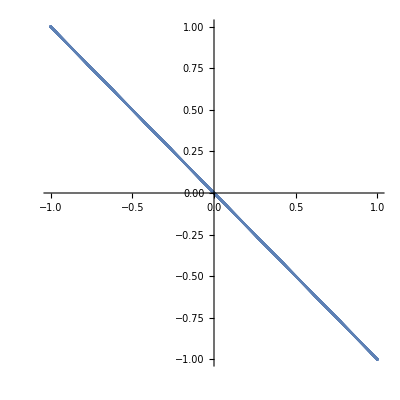

```mathematica
ParametricPlot[dcoeffy,{roll,-26.389378290154262,26.389378290154262}]
```

```mathematica
ParametricPlot[dcoeffy,{roll,-26.389378290154262,26.389378290154262}]
```

-Graphics-

```mathematica
dcoeffc = Simplify[denom - Dot[Transpose[{dcoeffx, dcoeffy}], {Tx, Ty}]]
```

{Ex Cos[pitch] Cos[roll]-Ez Cos[roll] Sin[pitch]-Ey Sin[roll],-Ex Cos[pitch] Cos[roll]+Ez Cos[roll] Sin[pitch]+Ey Sin[roll]}

```mathematica
rollMatrix
```

{{1,0,0},{0,Cos[roll],-Sin[roll]},{0,Sin[roll],Cos[roll]}}

```mathematica
Simplify[Solve[denom[[1]]==0, Tx]]
```

{{Tx→Ex-Ez Tan[pitch]-(Ey-Ty) Sec[pitch] Tan[roll]}}

```mathematica
Simplify[Ssolution, roll==0.023573848399758263 && pitch == 6.2828172583169373 &&
	Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853 
&& Cx==0.27823978575406083 && Cy==0.06996609351214557 && Cz==0.1741620789407514 && Tx==0 &&Ty == 0]
```

{{Sx→0.524096,Sy→0.439207}}

```mathematica
Simplify[Dot[Rb,{0.27883144,0.07262362,0.17211595}],  roll==0.015306584944257674 && pitch == 6.2797572862244362]
```

{0.27824,0.0699661,0.174162}

```mathematica
Simplify[coeffx, roll==0.023573848399758263 && pitch == 6.2828172583169373 &&
	Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853 
&& Cx==0.27823978575406083 && Cy==0.06996609351214557 && Cz==0.1741620789407514 && Tx==0 &&Ty == 0]
```

{-0.0121292,0.00034208}

```mathematica
Simplify[coeffc, roll==0.023573848399758263 && pitch == 6.2828172583169373 &&
	Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853 
&& Cx==0.27823978575406083 && Cy==0.06996609351214557 && Cz==0.1741620789407514 && Tx==0 &&Ty == 0]
```

{0.00108765,0.000911478}

```mathematica
Simplify[coeffc, roll==0.023573848399758263 && pitch == 6.2828172583169373 &&
	Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853 
&& Cx==0.27823978575406083 && Cy==0.06996609351214557 && Cz==0.1741620789407514 && Tx==0 &&Ty == 0]
```

```mathematica
Simplify[Dot[Rb,{0.27883144,0.07262362,0.17211595}],  roll==0.023573848399758263 && pitch == 6.2828172583169373]
```

{0.278767,0.0685464,0.173883}

```mathematica
Simplify[coeffx, roll==0.023573848399758263 && pitch == 6.2828172583169373 &&
	Ex== 0.04027264 && Ey == 0.08037242 && Ez == -0.05411853 
&& Cx==0.27823978575406083 && Cy==0.06854638198667043 && Cz==0.17388259899779715 && Tx==0 &&Ty == 0]
```

{-0.0121292,0.000419248}

```mathematica
coeffx
```

{Ez Cos[roll] (Ez+Cx Cos[pitch]-Cz Sin[pitch]),Ez (Cos[pitch] (-Ey+Cy Cos[roll])+(Cz-Ez Sin[pitch]) Sin[roll])}